Mode (n,k)

```mathematica
n=1;
rs = 0.01;
```

Zeros of the Bessel functions relate to the frequency ω and β

```mathematica
k=0;
f[x_, k_]=BesselJ[k, x]BesselI[k+1,x]+BesselI[k,x]BesselJ[k+1,x];
rootsNumeric = NSolve[{f[x, k]==0, 0 < x <= 100}, x, Reals] // N[#,10]&;
roots = x /. rootsNumeric;
StringReplace[ToString[NumberForm[roots, 10]],{"{"->"[","}"->"]"}]
```

[3.196220617, 6.306437048, 9.439499138, 12.57713064, 15.71643853, 18.85654552, 21.99709516, 25.13791541, 28.27891311, 31.42003345, 34.56124206, 37.70251633, 40.84384075, 43.98520433, 47.12659909, 50.26801907, 53.40945973, 56.55091758, 59.69238985, 62.83387435, 65.9753693, 69.11687326, 72.25838504, 75.39990364, 78.54142824, 81.68295814, 84.82449275, 87.96603155, 91.1075741, 94.24912002, 97.390669]

```mathematica
NN=5;
f[x_,l_]:=BesselJ[l,x]BesselI[l+1,x]+BesselI[l,x]BesselJ[l+1,x];
rootsArray = Table[
Module[{rootsNumeric, roots}, 
rootsNumeric=NSolve[{f[x,l]==0, 0<x<=200},x,Reals];
roots=x/.rootsNumeric;
If[Length[roots]>=NN, Take[roots,NN], roots]
],{l,0,12}
];
formattedOutput = StringReplace[ToString[NumberForm[rootsArray,10]],{"{"->"[","}"->"]"}]
```

[[3.196220617, 6.306437048, 9.439499138, 12.57713064, 15.71643853], [4.610899879, 7.799273801, 10.95806719, 14.10862781, 17.25572701], [5.905678235, 9.1968826, 12.40222097, 15.57949149, 18.7439581], [7.143531024, 10.53666987, 13.79506359, 17.00529018, 20.19231303], [8.346605939, 11.83671846, 15.1498701, 18.39595701, 21.60844831], [9.525701356, 13.10736371, 16.47507757, 19.7582766, 22.99787245], [10.68702586, 14.35515634, 17.77643378, 21.09712081, 24.36470172], [11.83453021, 15.58455188, 19.05805844, 22.41612475, 25.71210576], [12.97090865, 16.7987406, 20.32302126, 23.71808431, 27.04258559], [14.09809354, 18.00009791, 21.57368079, 25.00520347, 28.35815492], [15.21752515, 19.19044779, 22.81189466, 26.27925538, 29.66046293], [16.33031005, 20.37122616, 24.03915635, 27.54169121, 30.95088001], [17.43731958, 21.54358686, 25.25668738, 28.79371612, 32.23055928]]

Defining the mode function with Amplitude 1 and r_s = 1

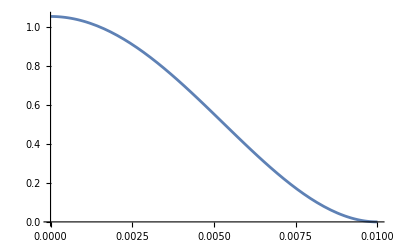

```mathematica
u[r_,θ_]=(BesselJ[k,roots[[n]]r/rs]-(BesselJ[k,roots[[n]]]/BesselI[k,roots[[n]]]) BesselI[k,roots[[n]]r/rs])Cos[k*θ];
Plot[u[r,0],{r,0,rs}]
(* ParametricPlot3D[{r Cos[θ], r Sin[θ],u[r,θ]},{r,0,rs}, {θ,0,2 Pi},Mesh->None, ColorFunction->"Rainbow"] *)
```

Find maximum / minimum of the gradient

```mathematica
gradient = D[u[r,0],r];
maxResult = Maximize[Abs[gradient], {r}∈Interval[{0,rs}]]
maximumGrad = First[maxResult]//N;
argmax = r/.Last[maxResult];
```

{163.378,{r→0.00527477}}

```mathematica
Maximize[Abs[u[r,0]],{r}∈Interval[{0,rs}]]
```

{1.05571,{r→0.}}

Find Amplitude

```mathematica
hbar=Quantity["ReducedPlanckConstant"];
kB =Quantity["BoltzmannConstant"];
T=Quantity[4,"Kelvins"];
m = Quantity[8960*Pi*rs^2*100*10^-9,"Kilograms"];
ω = Quantity[roots[[n]]^2/0.01^2*1.0727*10^-4,"Hertz"];
XVariance =UnitConvert[hbar/(2*m*ω)Coth[(hbar ω)/(2 kB T)],"Meters^2"]
DeltaX=Sqrt[XVariance]
```

2.81487×10^-7 kg

1.63374×10^-18 m^2

1.27818×10^-9 m

```mathematica
A = QuantityMagnitude[DeltaX];
```

Minimum angular variance θ and minimum length variance L due to thermal fluctuations

```mathematica
Varθ = ArcTan[A*maximumGrad]//N
```

2.08826×10^-7

```mathematica
VarL = A*u[argmax,0]//N
```

6.5062×10^-10

Particles sitting in the middle (for most modes this is not the worst case)

```mathematica
gradientMiddle = D[u[r,0],r] /. r ->0;
VarθMiddle = ArcTan[A*gradientMiddle]//N
VarLMiddle = A*u[0,0]//N
```

0.

1.34939×10^-9

```mathematica
Sum[1/k^8,{k, 1, 1}]*100/Zeta[8] //N
```

99.5939